## Load files with data

```mathematica
plotNames={"1s","1minute","1hour","24hours","1year"(*,"1week"*)};
filenames =FileNameJoin[{NotebookDirectory[],"u235time"<>#<>".dat"}]&/@plotNames;
data=Import[#,"Data"]&/@filenames;
Length[data]
```

5

## Neutrino spectrum plots

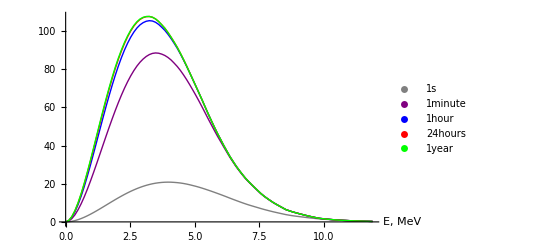

```mathematica
ListPlot[data,PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames]
```

## Normalized plots

```mathematica
dataNormalized={};
For[i=1,i≤Length[data],i++,
AppendTo[dataNormalized,
{#[[1]],#[[2]]/Max[data[[i]][[All,2]]]}&/@data[[i]]
]
]
```

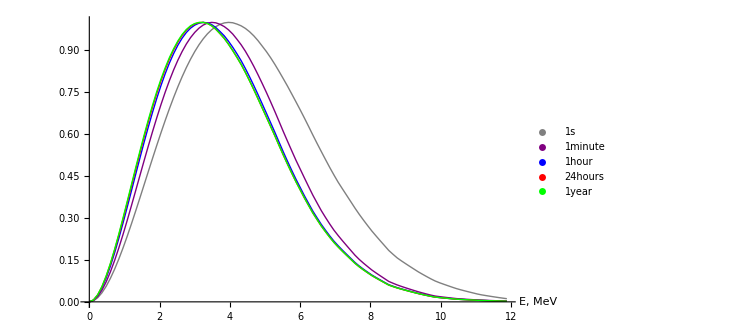

```mathematica
ListPlot[dataNormalized,PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames]
```